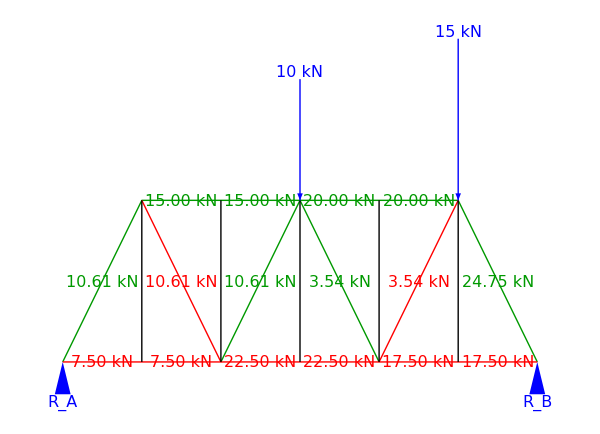

```mathematica
Module[{w,h,θ,rA,rB,F10,F11,F13,F16,F15,F17,F19,F20,F12,F8,F4,F7,F3,F5,F0,F2},
w=5;h=5;θ=ArcTan[h/w];

rB=r/.Solve[(3*w)*(-10)+(5*w)*(-15)+(6*w)*r==0][[1]];
rA=r/.Solve[r+rB-10-15==0,r][[1]];

F10=f/.Solve[-10+rA+f*Sin[θ]==0,f][[1]];
F11=f/.Solve[(3*w)*rA+(w)*f==0,f][[1]];
F13=f/.Solve[f+F10*Cos[θ]+F11==0,f][[1]];

F16=f/.Solve[rA-10+f*Sin[θ]==0,f][[1]];
F15=f/.Solve[(w)*f+(w)*(-10)+(4*w)*rA==0,f][[1]];
F17=f/.Solve[f+F15+F16*Cos[θ]==0,f][[1]];

F19=f/.Solve[rA-10-15+f*Sin[θ]==0,f][[1]];
F20=f/.Solve[f+F19*Cos[θ]==0,f][[1]];

F12=f/.Solve[rA+f*Sin[θ]==0,f][[1]];
F8=f/.Solve[(2*w)*rA+(w)*f==0,f][[1]];
F4=f/.Solve[F8+F12*Cos[θ]+f==0,f][[1]];

F7=f/.Solve[rA+f*Sin[θ]==0,f][[1]];
F3=f/.Solve[(w)*rA+(w)*f==0,f][[-1]];
F5=f/.Solve[f+F7*Cos[θ]+F3==0,f][[1]];

F0=f/.Solve[rA+f*Sin[θ]==0,f][[1]];
F2=f/.Solve[F0*Cos[θ]+f==0,f][[1]];

Text@Style[Grid[N@{{"F_0 =",F0},{"F_2 =",F2},{"F_3 =",F3},{"F_4 =",F4},{"F_5 =",F5},{"F_7 =",F7},{"F_8 =",F8},{"F_10 =",F10},{"F_11 =",F11},{"F_12 =",F12},{"F_13 =",F13},{"F_15 =",F15},{"F_16 =",F16},{"F_17 =",F17},{"F_19 =",F19},{"F_20 =",F20}}],18];

Graphics[{
{Thick,
RGBColor[0,0.6,0],Line[{{0,0},{w,h},{5*w,h},{6*w,0}}],Line[{{2*w,0},{3*w,h},{4*w,0}}],
Red,Line[{{0,0},{6*w,0}}],Line[{{w,h},{2*w,0}}],Line[{{4*w,0},{5*w,h}}],
Black,Line[{{#*w,0},{#*w,h}}]&/@Range@5,
Blue,Arrow[{{3*w,1.75*h},{3*w,h}}],Arrow[{{5*w,2*h},{5*w,h}}]},

Text[Style[Row@{#1," kN"},16,Blue],#2,{0,-1}]&@@@{{10,{3*w,1.75*h}},{15,{5*w,2*h}}},

{Blue,Polygon[{{#-0.1*w,-0.2*h},{#+0.1*w,-0.2*h},{#,0}}],Text[Style[Subscript[Style["R",Italic],If[#==0,"A","B"]],16],{#,-0.2*h},{0,1.5}]}&/@{0,6*w},

Text[Style[Row@{NumberForm[N@Abs@#1,{4,2}]," kN"},16,#3,Background->White],#2]&@@@{{F0,{w/2,h/2},RGBColor[0,0.6,0]},{F2,{w/2,0},Red},{F3,{1.5*w,0},Red},{F4,{2.5*w,0},Red},{F5,{1.5*w,h},RGBColor[0,0.6,0]},{F7,{1.5*w,h/2},Red},{F8,{2.5*w,h},RGBColor[0,0.6,0]},{F10,{3.5*w,h/2},RGBColor[0,0.6,0]},{F11,{3.5*w,0},Red},{F12,{2.5*w,h/2},RGBColor[0,0.6,0]},{F13,{3.5*w,h},RGBColor[0,0.6,0]},{F15,{4.5*w,h},RGBColor[0,0.6,0]},{F16,{4.5*w,h/2},Red},{F17,{4.5*w,0},Red},{F19,{5.5*w,h/2},RGBColor[0,0.6,0]},{F20,{5.5*w,0},Red}}
},ImageSize->{600,435}]
]
```

```mathematica
(*{EdgeForm@Thick,FaceForm@None,Polygon[{{#*w,0},{#*w+w,h},{#*w+2*w,0}}]&/@Range[0,5,2]},
{Thick,Line[{{w,h},{5*w,h}}],Line[{{#*w,0},{#*w,h}}]&/@Range@5},*)
```

```mathematica
(*Text[Style[Row@{N@#1," kN"},16,Background->White],#2]&@@@{{F0,{w/2,h/2}},{F2,{w/2,0}},{F3,{1.5*w,0}},{F4,{2.5*w,0}},{F5,{1.5*w,h}},{F7,{1.5*w,h/2}},{F8,{2.5*w,h}},{F10,{3.5*w,h/2}},{F11,{3.5*w,0}},{F12,{2.5*w,h/2}},{F13,{3.5*w,h}},{F15,{4.5*w,h}},{F16,{4.5*w,h/2}},{F17,{4.5*w,0}},{F19,{5.5*w,h/2}},{F20,{5.5*w,0}}}*)
```